```mathematica
ClearAll[kx,ky,k,processHijNew,trigExpansionRulesFull,separateExpFactors,simplifyExpArgs,getExpKxPower,filterByExponent,processMatrixEntry,Hraw2,Hfinal2];

(*Step 1:Define k-vector,  this has to be modified in different lattices , here it is a square lattice*)
k=kx {1,0}+ky {0,1};

(*Trig expansion rules  , expands all cos^2 and sin^2 terms*)
trigExpansionRulesFull={Cos[arg_]^2:>(1+Cos[2 arg])/2,Sin[arg_]^2:>(1-Cos[2 arg])/2,Cos[arg_]^3:>(3 Cos[arg]+Cos[3 arg])/4,Cos[a_] Cos[b_]:>1/2 (Cos[a+b]+Cos[a-b]),Sin[a_] Sin[b_]:>1/2 (Cos[a-b]-Cos[a+b]),Sin[a_] Cos[b_]:>1/2 (Sin[a+b]+Sin[a-b]),Cos[a_] Sin[b_]:>1/2 (Sin[a+b]-Sin[a-b])};

(*Trig to exponential form*)
cosToExp=Cos[arg_]:>1/2 (Exp[I arg]+Exp[-I arg]);
sinToExp=Sin[arg_]:>1/(2 I) (Exp[I arg]-Exp[-I arg]);

(*Separate exp factors involving kx and ky*)
separateExpFactors[expr_]:=expr//.{Exp[I (a_. kx+b_. ky)]:>Exp[I a kx] Exp[I b ky],Exp[I (a_. ky+b_. kx)]:>Exp[I b kx] Exp[I a ky],Exp[I (a_. kx)]:>Exp[I a kx],Exp[I (a_. ky)]:>Exp[I a ky]};

(*New function to simplify exponents in the form a kx+b ky*)
simplifyExpArgs[expr_]:=expr/. Exp[arg_]:>Exp[Expand[arg]];

(*Full pre-processing of the Hamiltonian matrix elements using previously defined functions  *)
processHijNew[expr_]:=Module[{step1,step2,step3},step1=expr/. trigExpansionRulesFull//Expand;
step2=step1/. {cosToExp,sinToExp}//Expand//Simplify;
step3=separateExpFactors[step2]//Expand;
simplifyExpArgs[step3]];


Hraw2={{-2+δ+Sin[Pi kx]^2,Sin[Pi kx] Sin[Pi ky],(m-t1 (Cos[Pi kx]+Cos[Pi ky])-t2 Cos[Pi (kx+ky)]) Sin[Pi kx]},{Sin[Pi kx] Sin[Pi ky],-2-δ+Sin[Pi ky]^2,(m-t1 (Cos[Pi kx]+Cos[Pi ky])-t2 Cos[Pi (kx+ky)]) Sin[Pi ky]},{(m-t1 (Cos[Pi kx]+Cos[Pi ky])-t2 Cos[Pi (kx+ky)]) Sin[Pi kx],(m-t1 (Cos[Pi kx]+Cos[Pi ky])-t2 Cos[Pi (kx+ky)]) Sin[Pi ky],-2+(-m+t1 (Cos[Pi kx]+Cos[Pi ky])+t2 Cos[Pi (kx+ky)])^2}};

(*Expand Hamiltonian*)
Hfinal2=Map[processHijNew,Hraw2,{2}];
MatrixForm[Hfinal2]
```

(-3/2-1/4 ⅇ^(-2 ⅈ kx π)-1/4 ⅇ^(2 ⅈ kx π) | -1/4 ⅇ^(-ⅈ kx π-ⅈ ky π)+1/4 ⅇ^(ⅈ kx π-ⅈ ky π)+1/4 ⅇ^(-ⅈ kx π+ⅈ ky π)-1/4 ⅇ^(ⅈ kx π+ⅈ ky π) | (0.+0.5 ⅈ) ⅇ^(-ⅈ kx π)-(0.+0.5 ⅈ) ⅇ^(ⅈ kx π)-(0.+0.25 ⅈ) ⅇ^(-2 ⅈ kx π)+(0.+0.25 ⅈ) ⅇ^(2 ⅈ kx π)-(0.+0.25 ⅈ) ⅇ^(-ⅈ kx π-ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(ⅈ kx π-ⅈ ky π)-(0.+0.25 ⅈ) ⅇ^(-ⅈ kx π+ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(ⅈ kx π+ⅈ ky π)
-1/4 ⅇ^(-ⅈ kx π-ⅈ ky π)+1/4 ⅇ^(ⅈ kx π-ⅈ ky π)+1/4 ⅇ^(-ⅈ kx π+ⅈ ky π)-1/4 ⅇ^(ⅈ kx π+ⅈ ky π) | -3/2-1/4 ⅇ^(-2 ⅈ ky π)-1/4 ⅇ^(2 ⅈ ky π) | (0.+0.5 ⅈ) ⅇ^(-ⅈ ky π)-(0.+0.5 ⅈ) ⅇ^(ⅈ ky π)-(0.+0.25 ⅈ) ⅇ^(-2 ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(2 ⅈ ky π)-(0.+0.25 ⅈ) ⅇ^(-ⅈ kx π-ⅈ ky π)-(0.+0.25 ⅈ) ⅇ^(ⅈ kx π-ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(-ⅈ kx π+ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(ⅈ kx π+ⅈ ky π)
(0.+0.5 ⅈ) ⅇ^(-ⅈ kx π)-(0.+0.5 ⅈ) ⅇ^(ⅈ kx π)-(0.+0.25 ⅈ) ⅇ^(-2 ⅈ kx π)+(0.+0.25 ⅈ) ⅇ^(2 ⅈ kx π)-(0.+0.25 ⅈ) ⅇ^(-ⅈ kx π-ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(ⅈ kx π-ⅈ ky π)-(0.+0.25 ⅈ) ⅇ^(-ⅈ kx π+ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(ⅈ kx π+ⅈ ky π) | (0.+0.5 ⅈ) ⅇ^(-ⅈ ky π)-(0.+0.5 ⅈ) ⅇ^(ⅈ ky π)-(0.+0.25 ⅈ) ⅇ^(-2 ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(2 ⅈ ky π)-(0.+0.25 ⅈ) ⅇ^(-ⅈ kx π-ⅈ ky π)-(0.+0.25 ⅈ) ⅇ^(ⅈ kx π-ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(-ⅈ kx π+ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(ⅈ kx π+ⅈ ky π) | -1. ⅇ^(-ⅈ kx π)-1. ⅇ^(ⅈ kx π)+0.25 ⅇ^(-2 ⅈ kx π)+0.25 ⅇ^(2 ⅈ kx π)-1. ⅇ^(-ⅈ ky π)-1. ⅇ^(ⅈ ky π)+0.25 ⅇ^(-2 ⅈ ky π)+0.25 ⅇ^(2 ⅈ ky π)+0.5 ⅇ^(-ⅈ kx π-ⅈ ky π)+0.5 ⅇ^(ⅈ kx π-ⅈ ky π)+0.5 ⅇ^(-ⅈ kx π+ⅈ ky π)+0.5 ⅇ^(ⅈ kx π+ⅈ ky π))

```mathematica
(*Define the variable representing a single step in x*)z=Exp[I Pi kx];

(*Function to extract the hopping matrix for a distance'n'*)
GetHoppingBlock[Hmatrix_,n_]:=Module[{temp},(*Replace Exp[I n Pi kx] with z^n*)temp=Hmatrix/. Exp[Complex[0,val_] Pi kx]:>z^(val);
(*Extract the coefficient of z^n*)Map[Coefficient[Expand[#],z,n]&,temp,{2}]];

(*Extract blocks*)
(*H0 is the'On-site' block (diagonal blocks in the ribbon)*)
H0=GetHoppingBlock[Hfinal2,0]

(*H1 is the'Nearest Neighbor' hopping (e.g.,x->x+a)*)
H1=GetHoppingBlock[Hfinal2,1]

Hm1 =GetHoppingBlock[Hfinal2,-1]


(*Hm1 is the hopping in the opposite direction (x->x+2a)*)
H2=GetHoppingBlock[Hfinal2,2]

(*Check Hermiticity of the components*)Hm1=GetHoppingBlock[Hfinal2,-1];
Hm2=GetHoppingBlock[Hfinal2,-2]

(*Assuming m,t1,t2,delta,ky are all real*)HermitianCheck[A_,B_]:=FullSimplify[A-ConjugateTranspose[B],Assumptions->Element[{m,t1,t2,δ,ky},Reals]]==ConstantArray[0,Dimensions[A]];

Print["H0 is Hermitian: ",HermitianCheck[H0,H0]];
Print["H-1 is H1 adjoint: ",HermitianCheck[Hm1,H1]];
Print["H-2 is H2 adjoint: ",HermitianCheck[Hm2,H2]];
```

{{-3/2,0,0.+0. ⅈ},{0,1/4 ⅇ^(-2 ⅈ ky π) (-1-6 ⅇ^(2 ⅈ ky π)-ⅇ^(4 ⅈ ky π)),(0.+0.25 ⅈ) ⅇ^(-2 ⅈ ky π) (-1.+2. ⅇ^(ⅈ ky π)-2. ⅇ^(3 ⅈ ky π)+ⅇ^(4 ⅈ ky π))},{0.+0. ⅈ,(0.+0.25 ⅈ) ⅇ^(-2 ⅈ ky π) (-1.+2. ⅇ^(ⅈ ky π)-2. ⅇ^(3 ⅈ ky π)+ⅇ^(4 ⅈ ky π)),0.25 ⅇ^(-2 ⅈ ky π) (1-4. ⅇ^(ⅈ ky π)-4. ⅇ^(3 ⅈ ky π)+ⅇ^(4 ⅈ ky π))}}

{{0,1/4 ⅇ^(-ⅈ ky π)-1/4 ⅇ^(ⅈ ky π),(0.-0.5 ⅈ)+(0.+0.25 ⅈ) ⅇ^(-ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(ⅈ ky π)},{1/4 ⅇ^(-ⅈ ky π)-1/4 ⅇ^(ⅈ ky π),0,(0.-0.25 ⅈ) ⅇ^(-ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(ⅈ ky π)},{(0.-0.5 ⅈ)+(0.+0.25 ⅈ) ⅇ^(-ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(ⅈ ky π),(0.-0.25 ⅈ) ⅇ^(-ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(ⅈ ky π),-1.+0.5 ⅇ^(-ⅈ ky π)+0.5 ⅇ^(ⅈ ky π)}}

{{0,-1/4 ⅇ^(-ⅈ ky π)+1/4 ⅇ^(ⅈ ky π),(0.+0.5 ⅈ)-(0.+0.25 ⅈ) ⅇ^(-ⅈ ky π)-(0.+0.25 ⅈ) ⅇ^(ⅈ ky π)},{-1/4 ⅇ^(-ⅈ ky π)+1/4 ⅇ^(ⅈ ky π),0,(0.-0.25 ⅈ) ⅇ^(-ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(ⅈ ky π)},{(0.+0.5 ⅈ)-(0.+0.25 ⅈ) ⅇ^(-ⅈ ky π)-(0.+0.25 ⅈ) ⅇ^(ⅈ ky π),(0.-0.25 ⅈ) ⅇ^(-ⅈ ky π)+(0.+0.25 ⅈ) ⅇ^(ⅈ ky π),-1.+0.5 ⅇ^(-ⅈ ky π)+0.5 ⅇ^(ⅈ ky π)}}

{{-1/4,0,0.+0.25 ⅈ},{0,0,0},{0.+0.25 ⅈ,0,0.25}}

{{-1/4,0,0.-0.25 ⅈ},{0,0,0},{0.-0.25 ⅈ,0,0.25}}

H0 is Hermitian: True

H-1 is H1 adjoint: True

H-2 is H2 adjoint: True

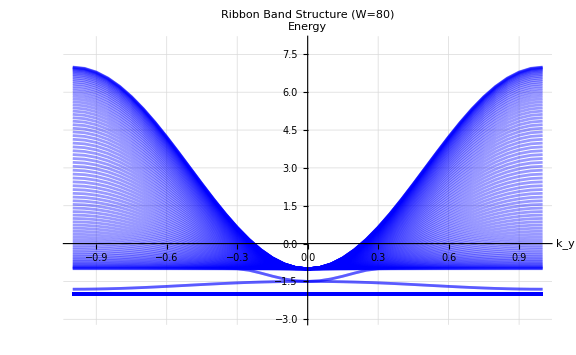

```mathematica
BuildRibbonMat[kInput_,W_Integer]:=Module[{h0,h1,h2,hm1,hm2,rules},rules={ky->kInput};
(*Substitution must happen inside the module using the input value*){h0,h1,h2,hm1,hm2}={H0,H1,H2,Hm1,Hm2}/. rules;
ArrayFlatten[Table[Which[i==j,h0,j==i+1,h1,j==i-1,hm1,j==i+2,h2,j==i-2,hm2,True,ConstantArray[0,{3,3}]],{i,1,W},{j,1,W}]]];

(*Define Numerical Constants*)m=1.0;t1=1.0;t2=0;δ=0;
W=80; (*Number of unit cells in the x-direction*)
kyVals=Range[-1,1,0.05]; (*k-points along the infinite direction*)

(*Share definitions with Parallel Kernels*)
DistributeDefinitions[H0,H1,H2,Hm1,Hm2,BuildRibbonMat,m,t1,t2,δ];

(*Compute Eigenvalues*)eigenvalsListSorted=ParallelMap[Sort[Re[Eigenvalues[N[BuildRibbonMat[#,W]]]]]&,kyVals];

(*Formatting and Visualization*)numBands=3*W;


bandData=Table[Transpose[{kyVals,eigenvalsListSorted[[All,i]]}],{i,1,numBands}];



ListPlot[bandData,Joined->True,PlotRange->{-3,8}, PlotStyle->Directive[Opacity[0.4],Blue],AxesLabel->{"\!\(\*SubscriptBox[\(k\), \(y\)]\)","Energy"},



PlotLabel->"Ribbon Band Structure (W="<>ToString[W]<>")",ImageSize->Large,GridLines->Automatic]
```